```mathematica
SeedRandom[20230402];
data=Table[RandomVariate[NormalDistribution[μ,5],100],{μ,-6,6,2}];
```

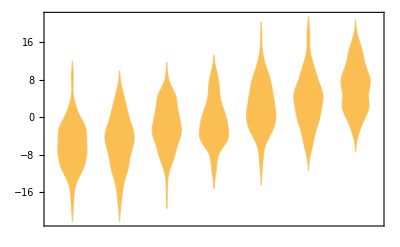

```mathematica
DistributionChart[data]
```

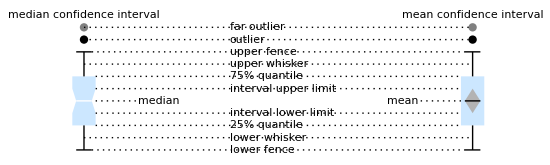

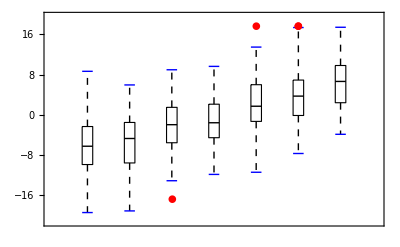

```mathematica
BoxWhiskerChart[
data,{{"MedianMarker",1,Directive[Black,Thickness->0.008]},{"Outliers","●",Red},{"Whiskers",Directive[Dashed]},{"Fences",1,Directive[Blue,Thickness->0.003]}},BarSpacing->3,ChartStyle-> Directive[EdgeForm[Black],White]]
```

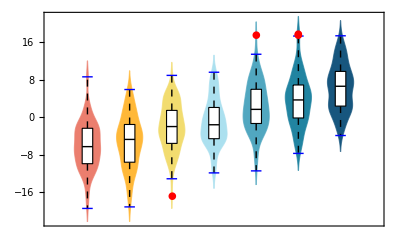

```mathematica
Show[
DistributionChart[data,ChartStyle->24],
BoxWhiskerChart[data,
{{"MedianMarker",1,Directive[Black,Thickness->0.008]},
{"Outliers","●",Red},
{"Whiskers",Directive[Dashed]},
{"Fences",1,Directive[Blue,Thickness->0.003]}},
BarSpacing->3,
ChartStyle-> Directive[EdgeForm[Black],White]]]
```

```mathematica
datax=Table[RandomVariate[NormalDistribution[0,1],200]+Table[Sin[j],{i,1,200}],{j,1,7}];
datay=Table[RandomVariate[NormalDistribution[0,1],200]+Table[Cos[j],{i,1,200}],{j,1,7}];
data2={datax,datay}//Transpose;
```

```mathematica
cEF[f_:"BoxWhisker",w_:.5]:={ChartElementData[f][{Mean@#[[1]]+{-w,w}/2,#[[2]]},##2]}&
```

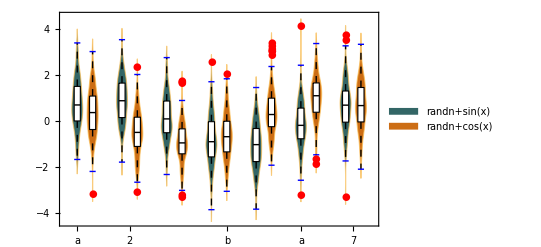

```mathematica
Show[DistributionChart[data2,BarSpacing->#,ChartStyle->89,ChartLegends->{"randn+sin(x)","randn+cos(x)"},ChartLabels->{{"1","2","3","4","5","6","7"},{"a","b"}}],BoxWhiskerChart[
data2,{{"MedianMarker",1,Directive[Black,Thickness->0.008]},{"Outliers","●",Red},{"Whiskers",Directive[Dashed]},{"Fences",1,Directive[Blue,Thickness->0.003]}},BarSpacing->#,ChartStyle-> Directive[EdgeForm[Black],White],ChartElementFunction->cEF["BoxWhisker",0.4]]]&[{0.4,1.2}]
```

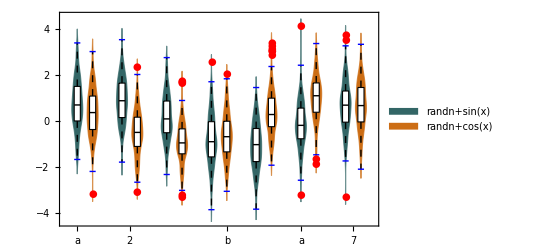

```mathematica
Show[
DistributionChart[data2,
BarSpacing->#,
ChartStyle->89,
ChartLegends->SwatchLegend[{"randn+sin(x)","randn+cos(x)"},
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,True}}]&)],
ChartLabels->{{"1","2","3","4","5","6","7"},{"a","b"}}],
BoxWhiskerChart[data2,
{{"MedianMarker",1,Directive[Black,Thickness->0.008]},
{"Outliers","●",Red},{"Whiskers",Directive[Dashed]},
{"Fences",1,Directive[Blue,Thickness->0.003]}},
BarSpacing->#,
ChartStyle-> Directive[EdgeForm[Black],White],
ChartElementFunction->cEF["BoxWhisker",0.4]]]&[{0.4,1.2}]
```

```mathematica
datax=Table[RandomVariate[NormalDistribution[0,1],200]+Table[Sin[j],{i,1,200}],{j,1,7}];
datay=Table[RandomVariate[NormalDistribution[0,1],200]+Table[Cos[j],{i,1,200}],{j,1,7}];
data2={datax,datay}//Transpose;
```

```mathematica
data3=(Table[RandomVariate[NormalDistribution[0,1],200]+Table[#[j],{i,1,200}],{j,1,7}]&/@{Sqrt,Log,Tan,Csc})//Transpose;
```

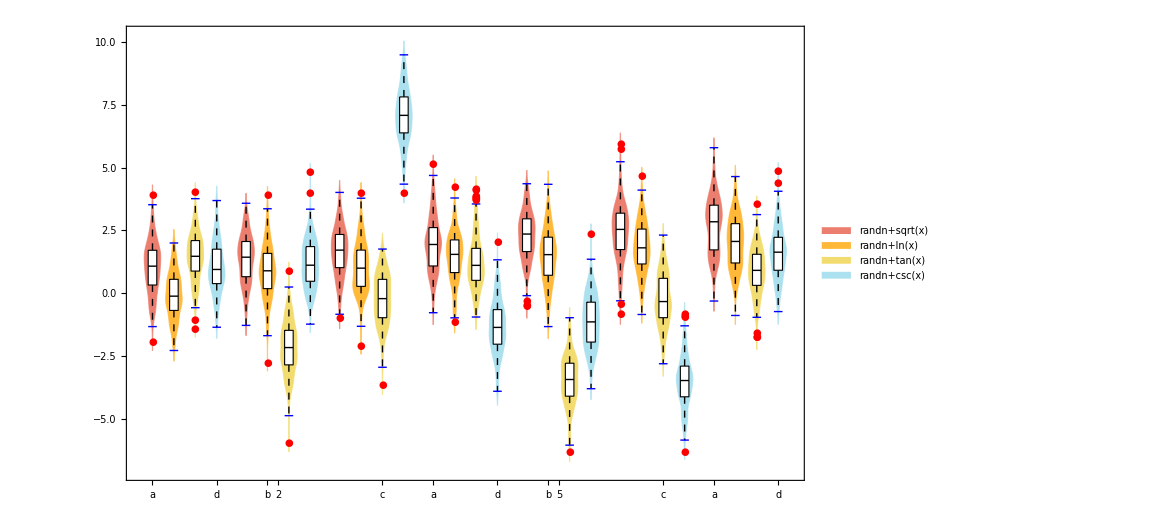

```mathematica
Show[
DistributionChart[data3,
BarSpacing->#,
ChartStyle->24,
ChartLegends->SwatchLegend[{"randn+sqrt(x)","randn+ln(x)","randn+tan(x)","randn+csc(x)"},
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,False,False,True}}]&)],
ChartLabels->{{"1","2","3","4","5","6","7"},{"a","b","c","d"}}],
BoxWhiskerChart[data3,
{{"MedianMarker",1,Directive[Black,Thickness->0.008]},
{"Outliers","●",Red},{"Whiskers",Directive[Dashed]},
{"Fences",1,Directive[Blue,Thickness->0.003]}},
BarSpacing->#,
ChartStyle-> Directive[EdgeForm[Black],White],
ChartElementFunction->cEF["BoxWhisker",0.4]]]&[{0.3,0.6}]
```

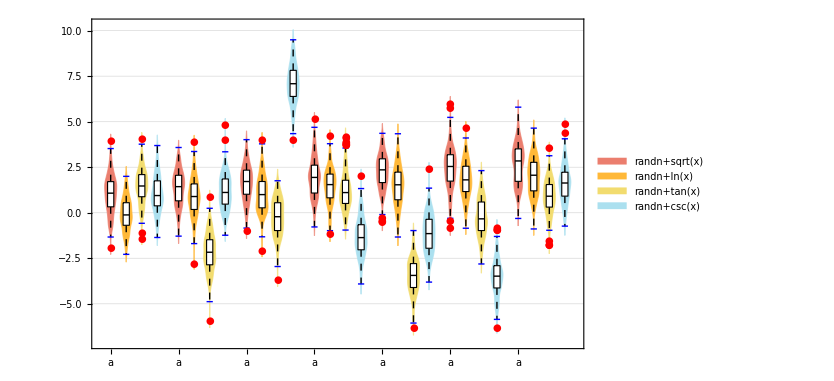

```mathematica
Show[
DistributionChart[data3,
BarSpacing->#,
ChartStyle->24,
ChartLegends->SwatchLegend[{"randn+sqrt(x)","randn+ln(x)","randn+tan(x)","randn+csc(x)"},
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,False,False,True}}]&)],
ChartLabels->{{"1","2","3","4","5","6","7"},{"a","b","c","d"}},PlotTheme->#2],
BoxWhiskerChart[data3,
{{"MedianMarker",1,Directive[Black,Thickness->0.008]},
{"Outliers","●",Red},{"Whiskers",Directive[Dashed]},
{"Fences",1,Directive[Blue,Thickness->0.003]}},
BarSpacing->#,
ChartStyle-> Directive[EdgeForm[Black],White],
ChartElementFunction->cEF["BoxWhisker",0.4]],PlotTheme->#2]&[{0.3,0.6},"Detailed"]
```

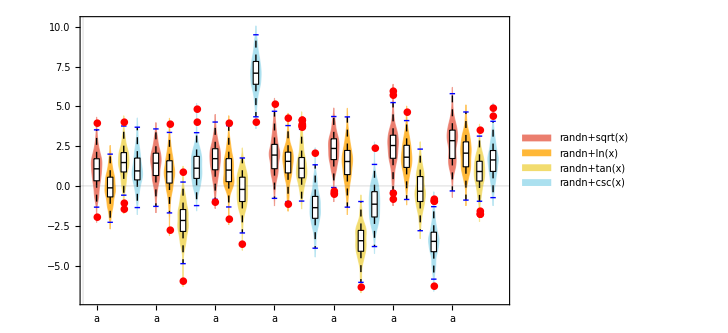

```mathematica
Show[
DistributionChart[data3,
BarSpacing->#,
ChartStyle->24,
ChartLegends->SwatchLegend[{"randn+sqrt(x)","randn+ln(x)","randn+tan(x)","randn+csc(x)"},
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,False,False,True}}]&)],
ChartLabels->{{"1","2","3","4","5","6","7"},{"a","b","c","d"}},PlotTheme->#2],
BoxWhiskerChart[data3,
{{"MedianMarker",1,Directive[Black,Thickness->0.008]},
{"Outliers","●",Red},{"Whiskers",Directive[Dashed]},
{"Fences",1,Directive[Blue,Thickness->0.003]}},
BarSpacing->#,
ChartStyle-> Directive[EdgeForm[Black],White],
ChartElementFunction->cEF["BoxWhisker",0.4]],PlotTheme->#2]&[{0.3,0.6},"Scientific"]
```

```mathematica
data4=(Table[RandomVariate[NormalDistribution[0,1],200]+Table[#[j],{i,1,200}],{j,1,4}]&/@{Sin,Cos})//Transpose;
```

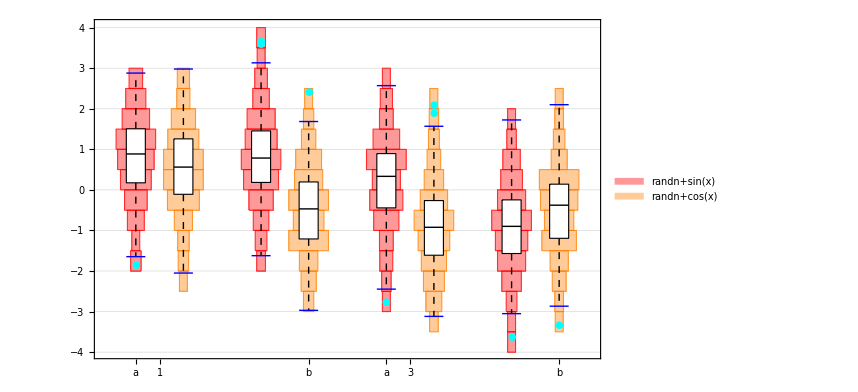

```mathematica
Show[
DistributionChart[data4,
BarSpacing->#,
ChartStyle->{Red,Orange},
ChartLegends->SwatchLegend[{"randn+sin(x)","randn+cos(x)"},
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,True}}]&)],
ChartLabels->{{"1","2","3","4"},{"a","b"}},
PlotTheme->#2,
ChartElementFunction->"HistogramDensity",
ChartBaseStyle->Directive[EdgeForm[Thin],Opacity[0.4]]],
BoxWhiskerChart[data4,
{{"MedianMarker",1,Directive[Black,Thickness->0.008]},
{"Outliers","●",RGBColor[0,1,1]},{"Whiskers",Directive[Dashed]},
{"Fences",1,Directive[Blue,Thickness->0.003]}},
BarSpacing->#,
ChartStyle-> Directive[EdgeForm[Black],White],
ChartElementFunction->cEF["BoxWhisker",0.4],
PlotTheme->#2]]&[{0.2,0.8},"Detailed"]
```

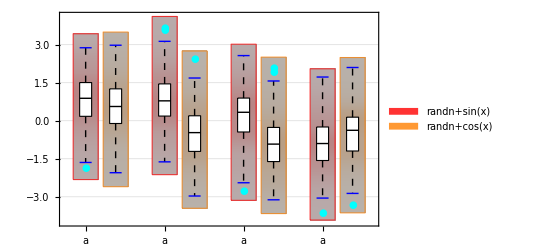

```mathematica
Show[
DistributionChart[data4,
BarSpacing->#,
ChartStyle->{Red,Orange},
ChartLegends->SwatchLegend[{"randn+sin(x)","randn+cos(x)"},
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,True}}]&)],
ChartLabels->{{"1","2","3","4"},{"a","b"}},
PlotTheme->#2,
ChartElementFunction->"Density",
ChartBaseStyle->Directive[EdgeForm[Thin],Opacity[0.8]]],
BoxWhiskerChart[data4,
{{"MedianMarker",1,Directive[Black,Thickness->0.008]},
{"Outliers","●",RGBColor[0,1,1]},{"Whiskers",Directive[Dashed]},
{"Fences",1,Directive[Blue,Thickness->0.003]}},
BarSpacing->#,
ChartStyle-> Directive[EdgeForm[Black],White],
ChartElementFunction->cEF["BoxWhisker",0.4],
PlotTheme->#2]]&[{0.2,0.8},"Detailed"]
```

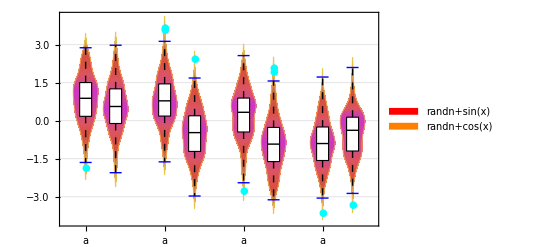

```mathematica
Show[
DistributionChart[data4,
BarSpacing->#,
ChartStyle->{Red,Orange},
ChartLegends->SwatchLegend[{"randn+sin(x)","randn+cos(x)"},
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,True}}]&)],
ChartLabels->{{"1","2","3","4"},{"a","b"}},
PlotTheme->#2,
ChartElementFunction->ChartElementData["SmoothDensity","ColorScheme"->"NeonColors"],
ChartBaseStyle->Directive[EdgeForm[Thin]]],
BoxWhiskerChart[data4,
{{"MedianMarker",1,Directive[Black,Thickness->0.008]},
{"Outliers","●",RGBColor[0,1,1]},{"Whiskers",Directive[Dashed]},
{"Fences",1,Directive[Blue,Thickness->0.003]}},
BarSpacing->#,
ChartStyle-> Directive[EdgeForm[Black],White],
ChartElementFunction->cEF["BoxWhisker",0.4],
PlotTheme->#2]]&[{0.2,0.8},"Detailed"]
```

```mathematica
Show[
DistributionChart[data,ChartStyle->24,ChartLegends->BarLegend[{"NeonColors",{0,1}},
LegendLayout->"Column"],
ChartLabels->{"1","2","3","4","5","6","7"},
PlotTheme->#,
ChartElementFunction->ChartElementData["SmoothDensity","ColorScheme"->"NeonColors"],
ChartBaseStyle->Directive[EdgeForm[Thin]]],
BoxWhiskerChart[data,
{{"MedianMarker",1,Directive[Black,Thickness->0.008]},
{"Outliers","●",Green},
{"Whiskers",Directive[Dashed]},
{"Fences",1,Directive[Blue,Thickness->0.003]}},
BarSpacing->3,
ChartStyle-> Directive[EdgeForm[Black],White],PlotTheme->#]]&["Detailed"]
```

-Graphics-

```mathematica
ClearAll[BoxWhiskerDistributionChart]
Options[BoxWhiskerDistributionChart]={"InternalOpacity"->0.7,"PointsToHighlight"->{},"PointToHighlightColor"->Red,"UpperCutoff"->.75,"LowerCutoff"->.25,"EdgeColor"->Charting`ChartStyleInformation["Color"]};

BoxWhiskerDistributionChart[{{xmin_,xmax_},{ymin_,ymax_}},values_,metadata_,OptionsPattern[]]:=Module[{chartParameters=Sequence[{{xmin,xmax},{ymin,ymax}},values,metadata]},{(*Give boxes thin edges with black color*)EdgeForm[{Thin,Black}],(*Alter boxes internal opacity with their respective color*)FaceForm[Opacity[OptionValue["InternalOpacity"],Charting`ChartStyleInformation["Color"]]],(*Use smooth density to change box shape,with given quantile cutoffs*)ChartElementDataFunction["SmoothDensity"][chartParameters]/. GeometricTransformation[Polygon[x_,y___],transformation_]:>Polygon[DeleteCases[AffineTransform[transformation]@x,{_,_?((#<Quantile[values,OptionValue["LowerCutoff"]]||#>Quantile[values,OptionValue["UpperCutoff"]])&)}],y],Opacity[1],(*Color points also foudn in the PointsToHighlight option*)ChartElementDataFunction["PointDensity","PointStyle"->PointSize[0.004]][chartParameters]/. GraphicsGroup[{x_,y__}]:>({y}/. Point[p_]:>(({If[MemberQ[OptionValue["PointsToHighlight"],#[[2]]],OptionValue["PointToHighlightColor"]],Point[{#}]}&/@p))),(*Remove the default BoxWhiskerChart EdgeForm*)EdgeForm[],(*Remove the default BoxWhiskerChart FaceForm*)FaceForm[](*Produce the plot*)}]
```

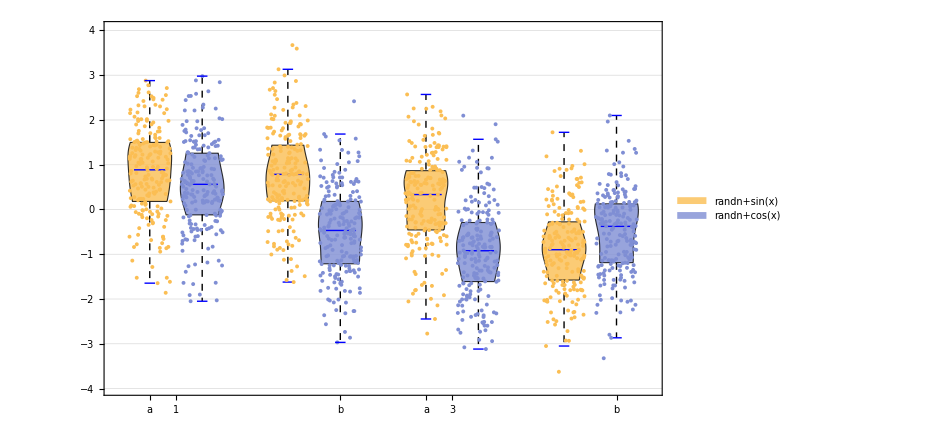

```mathematica
Show[DistributionChart[data4,
BarSpacing->#,
ChartLegends->SwatchLegend[{"randn+sin(x)","randn+cos(x)"},
LegendLayout->(Grid[Join[{{"Func",SpanFromLeft}},#],
Dividers->{{True,False,True},{True,True,False,True}}]&)],
ChartLabels->{{"1","2","3","4"},{"a","b"}},
PlotTheme->#2,
ChartElementFunction->(BoxWhiskerDistributionChart[##,"PointsToHighlight"->data4]&),
ChartBaseStyle->Directive[EdgeForm[{Thick,Black}],Opacity[0.8]],ImageSize->700],
BoxWhiskerChart[data4,
{{"MedianMarker",3,Directive[Blue,Thickness->0.002,Opacity[1]]},
{"Outliers","●",Red},{"Whiskers",Directive[Dashed,Opacity[1]]},
{"Fences",1,Directive[Blue,Thickness->0.003,Opacity[1]]}},
BarSpacing->#,
ChartStyle-> Directive[EdgeForm[None],Opacity[0]],
ChartElementFunction->cEF["BoxWhisker",0.2],
PlotTheme->#2]]&[{0.2,0.8},"Detailed"]
```

```mathematica
Options[plotGrid]={ImagePadding->40,"KeepAR"->False};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=If[OptionValue["KeepAR"],Module[{arfunc,arlist,tot},arfunc[img_]:=Module[{dims},dims=ImageDimensions[Show[img,ImagePadding->{{0,0},{0,0}}]];
N@dims[[1]]/dims[[2]]];
arlist=arfunc/@l[[1]];
tot=Total[arlist];
Table[arlist[[n]] (w-2 sidePadding)/tot,{n,nx}]],(w-2 sidePadding)/nx Table[1,{nx}]];
(*widths=(w-2 sidePadding)/nx Table[1,{nx}];*)widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=If[OptionValue["KeepAR"],Module[{arfunc,arlist,tot},arfunc[img_]:=Module[{dims},dims=ImageDimensions[Show[img,ImagePadding->{{0,0},{0,0}}]];
N@dims[[2]]/dims[[1]]];
arlist=arfunc/@l[[All,1]];
tot=Total[arlist];
Table[arlist[[-n]] (h-2 sidePadding)/tot,{n,ny}]],(h-2 sidePadding)/ny Table[1,{ny}]];
(*heights=(h-2 sidePadding)/ny Table[1,{ny}];*)heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]];
```

```mathematica
data5={RandomVariate[NormalDistribution[50,10],100],RandomVariate[NormalDistribution[20,1],100],RandomVariate[NormalDistribution[80,5],100]};
```

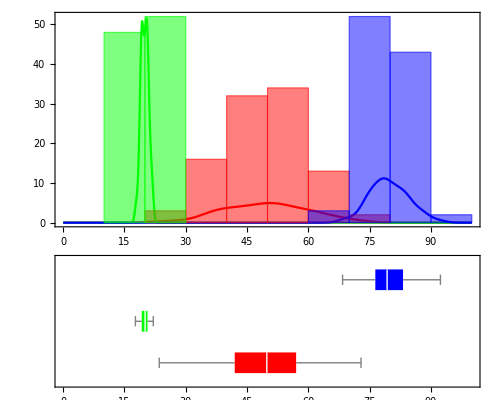

```mathematica
hist=Show[Plot[140 PDF[SmoothKernelDistribution[#],x]&/@data5,{x,0,100},Evaluated->True,PlotStyle->{Red,Green,Blue},Frame->True,PlotRange->{{0,100},All}],Histogram[data5,ChartStyle->{Red,Green,Blue}]];
bxchrt=BoxWhiskerChart[data5,BarOrigin->Left,AspectRatio->1/3,ChartStyle->{Red,Green,Blue},PlotRange->{First@Charting`get2DPlotRange@hist,All},PlotRangePadding->None];
plotGrid[{{hist},{bxchrt}},500,400,"KeepAR"->True]
```